```mathematica
data1=Import["/Users/stshammi/temp/EDGB_bound/posterior_1000.csv","CSV"] ;(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
data2=Import["/Users/stshammi/temp/EDGB_bound/monte-carlo--1pn-beta.csv","CSV"] ;
```

```mathematica
m1=data1[[All,5]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
m2=data1[[All,6]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
χ1=data1[[All,7]];
```

```mathematica
χ2=data1[[All,8]];
```

```mathematica
s1=2/χ1^2*(√(1-χ1^2)-1+χ1^2);
```

```mathematica
s2=2/χ2^2*(√(1-χ2^2)-1+χ2^2);
```

```mathematica
ζ=Abs[-7168/5*((m1+m2)^4*η^(18/5))/(((m1^2*s2)-(m2^2*s1))^2)*βppE]; (*Eqn. 29 of 1809.00259*)
```

```mathematica
ζSelected=Select[ζ,# <1 &];
```

```mathematica
Length[ζSelected]
```

683

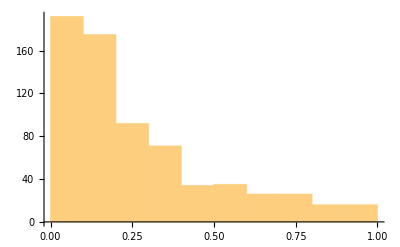

```mathematica
Histogram[ζSelected]
```

```mathematica
Mean[ζSelected]
```

0.26991

```mathematica
StandardDeviation[ζSelected]
```

0.236114

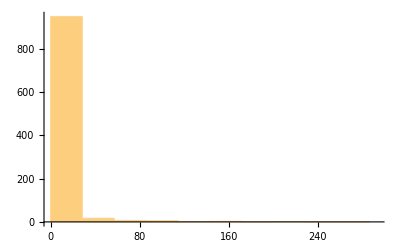

```mathematica
Histogram[ζ]
```

```mathematica
Mean[ζ]
```

99.0522

```mathematica
StandardDeviation[ζ]
```

1328.94

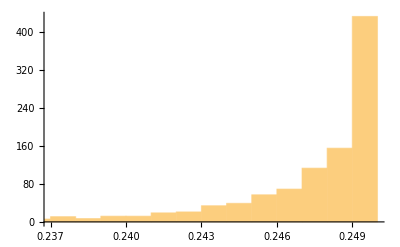

```mathematica
Histogram[η]
```

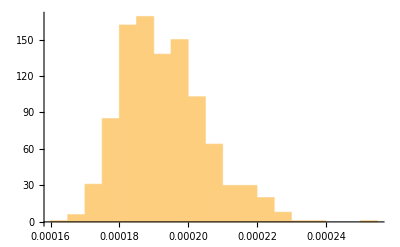

```mathematica
Histogram[m1]
```

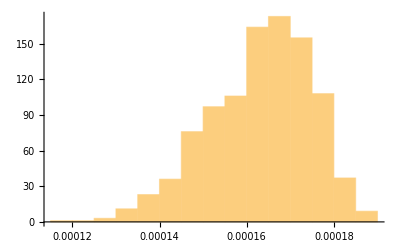

```mathematica
Histogram[m2]
```

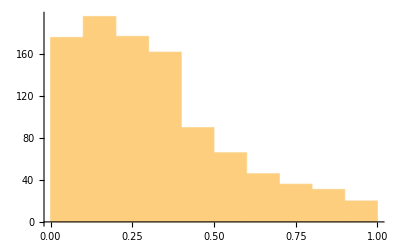

```mathematica
Histogram[χ1]
```

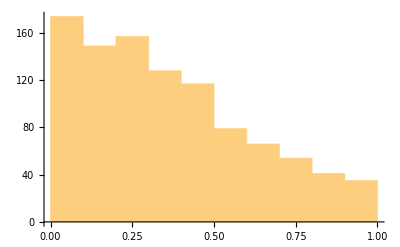

```mathematica
Histogram[χ2]
```